# Práctica 1 Curso 23 / 24

## Resolución de problemas de Programación Lineal. Dualidad. Cálculo de múltiples óptimos

## Introducción

### Instrucciones matriciales con Mathematica

La forma de definir el vector v de componentes v1 y v2 es:

```mathematica
v = {v1, v2}
```

La forma de definir una matriz A=(a | b
c | d) es:

```mathematica
A={{a,b},{c,d}}
```

Algunas operaciones básicas con matrices son:

```mathematica
A+B, A.B, Inverse[A], Transpose[A], Det[A]
```

### Ejercicio:

Define dos matrices cuadradas regulares de tamaño 2,  A y B, evalúalas y calcula su suma, su producto, sus inversas, sus traspuestas y sus determinantes.
Define una matriz F que no sea regular y trata de calcular su inversa.

```mathematica
A={{1, 2}, {3, 1}} (*Si ponemos ; al final no pone la salida. Pero sí se ejecuta la sentencia.*)
```

{{1,2},{3,1}}

```mathematica
B={{3, -1}, {5, -4}}
```

{{3,-1},{5,-4}}

```mathematica
A+B
```

{{4,1},{8,-3}}

```mathematica
A.B
```

{{13,-9},{14,-7}}

```mathematica
Inverse[A]
```

{{-1/5,2/5},{3/5,-1/5}}

```mathematica
Inverse[B]
```

{{4/7,-1/7},{5/7,-3/7}}

```mathematica
Transpose[A]
```

{{1,3},{2,1}}

```mathematica
Transpose[B]
```

{{3,5},{-1,-4}}

```mathematica
Det[A]
```

-5

```mathematica
Det[B]
```

-7

## Resolución de problemas de Programación Lineal

Mathematica tiene una gran colección de algoritmos para resolver problemas de Optimización con variables reales, accesibles con las instrucciones LinearProgramming, FindMinimum, FindMaximum, NMinimize, NMaximize, Minimize y Maximize.
La instrucción LinearProgramming es la que accede directamente a algoritmos de Programación Lineal. 
Las demás instrucciones resuelven problemas de Optimización, no necesariamente lineales. 
Vamos a ver cómo se utiliza cada uno de ellos:

-Graphics-

En esta práctica nos restringiremos solamente a la instrucción LinearProgramming

```mathematica
LinearProgramming[c,A,b] (*vector A, matriz A, vector B*)
```

encuentra un vector x que minimiza c' x sujeto a que Ax ≥ b y x ≥ 0.

Ejemplo: Min (x +2 y) , s.a.  -x + 3 y ≥1,-2x+y≥4, x ≥ 0, y≥ 0

```mathematica
c={1, 2}; A = {{-1, 3}, {-2, 1}}; b = {1, 4};
```

```mathematica
LinearProgramming[c, A, b]
```

{0,4}

```mathematica
LinearProgramming[c,A,{{b1,r1},{b2,r2},...}] 
(*
Tipo de desigualdad: ri = {1, -1 , 0}
0 -> =,
	1 -> >=,
	-1 -> <=
*)
```

encuentra un vector x que minimiza c' x sujeto a que x ≥ 0 y sujeto a las restricciones lineales especificadas por la matriz A y los pares {bi , ri} de la siguiente forma. Para cada fila ai de A, la correspondiente restricción es ai · x ≥ bi si ri = 1,  ai · x = bi si ri = 0 y ai · x ≤ bi si ri = -1.

Ejemplo:Min (x+y), s.a. x+2 y≥3, x-y≤2,x≥0, y≥0

```mathematica
LinearProgramming[{1, 1}, {{1, 2}, {1, -1}}, {{3, 1}, {2, -1}}]
```

{0,3/2}

```mathematica
LinearProgramming[c,A, b,{l1,l2,...}](*añadir cota inferior*)
```

encuentra un vector x que minimiza c' x sujeto a que Ax ≥ b, xi≥li.

Ejemplo:Min (x+y), s.a. x+2 y≥3, x-y≤2,x≥-1, y≥-1

```mathematica
LinearProgramming[{1, 1}, {{1, 2}, {1, -1}}, {{3, 1}, {2, -1}}, {-1, -1}]
```

{-1,2}

```mathematica
LinearProgramming[c,A, b,{{l1,u1},{l2,u2},...}](*añadir cota inf & sup*)
```

encuentra un vector x que minimiza c’ x sujeto a que Ax ≥ b  y li ≤ x ≤ ui.

Ejemplo:Min (x+y), s.a. x+2 y≥3,x-y≤2, -1≤ x≤1, -1≤ y ≤ 2

```mathematica
LinearProgramming[{1, 1}, {{1, 2}, {1, -1}}, {{3, 1}, {2, -1}}, {{-1, 1}, {-1, 2}}]
```

{-1,2}

```mathematica
LinearProgramming[c,A,b,Automatic, dom]
(*
   Automatic: no hay cotas (sólo no negativ.) 
Dom -> Dominio de las variables (Real, Integers)
*)
```

encuentra un vector x que minimiza c’ x sujeto a que Ax ≥ b, x ≥ 0 y x en el dominio dom (Reals, Integers, etc)

Ejemplo:Min (x+y), s.a. x+2 y≥3,x-y≤2,x≥0,y ≥  0, x e y enteras

```mathematica
LinearProgramming[{1, 1}, {{1, 2}, {1, -1}}, {{3, 1}, {2, -1}}, Automatic, Reals]
```

{0,3/2}

```mathematica
LinearProgramming[c,A,b, Automatic,{dom1,dom2,...}](*dominio por variable*)
```

encuentra un vector x que minimiza c’ x sujeto a que Ax ≥ b,  x ≥ 0 y xi en el dominio dom (Reals, Integers, etc)

Ejemplo:Min (x+y), s.a. x+2 y≥3,x-y≤2,x≥0,y ≥  0, x entera.

```mathematica
LinearProgramming[{1, 1}, {{1, 2}, {1, -1}}, {{3, 1}, {2, -1}}, Automatic, {Integers, Reals}]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{0,1.5}

```mathematica
LinearProgramming[c,A,b, Method->met]
(*
	Automatic: no usa método
  Simplex: simplex
  InteriorPoint: algoritmo del puntos interiores
*)
```

encuentra un vector x que minimiza c’ x sujeto a que Ax ≥ b y  x ≥ 0 utilizando el método met. Los posibles métodos son: Automatic, "Simplex", "RevisedSimplex" e "InteriorPoint".

## Problema ilimitado:

```mathematica
LinearProgramming[{2,1},{{3,2},{2,4}},{{6,-1},{5,-1}},{{0, Infinity},{-Infinity,Infinity}}] 
(*Min 2x + y, sa. 3x+2y<=6, 2x+4y<=5, 
x>=0, -Infinity <= y <= Infinity-*)
```

LinearProgramming::lpsub: This problem is unbounded.

{Indeterminate,Indeterminate}

## Problema imposible:

```mathematica
LinearProgramming[{-6,-8},{{3,2},{2,4}},{{2,-1},{1,0}},{{-Infinity,0},{-Infinity,0}}]
(*Min -6x-8y, sa 3x+2y<=2,2x+4y=1, x<=0, y<=0*)
```

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{-6,-8},{{3,2},{2,4}},{{2,-1},{1,0}},{{-∞,0},{-∞,0}}]

RegionPlot[pred, {x,xmin,xmax},{y,ymin, ymax}] representa un gráfico en el que "pred" es cierta, para los valores de las variables dados.

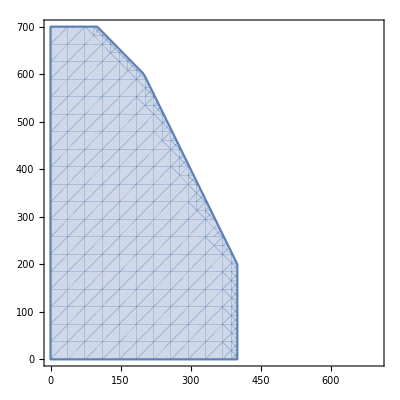

```mathematica
RegionPlot[x1+x2≤800&&2x1+x2≤1000&&x1≤400&&x2≤700&&x1>=0&&x2≥0,{x1,0,700},{x2,0,700}]
```

RegionPlot3D[pred, {x,xmin,xmax},{y,ymin,ymax},{z,zmin,zmax}] representa un gráfico tridimensional  en el que "pred" es cierta, para los valores de las variables dados.

```mathematica
RegionPlot3D[3x1+6x2+2x3≤6750&&x1≤1000&&x2≤500&&x3≤1500&&x1≥0&&x2≥0&&x3≥0,{x1,0,1500},{x2,0,1500},{x3,0,1500},PlotStyle->Directive[Automatic,Opacity[0.5]],Mesh->None]
```

-Graphics3D-

## Comentarios acerca de los métodos del simplex y de puntos interiores:

La  siguiente instrucción resuelve un problema de P. L. que tiene mútiples óptimos (cualquier punto del segmento que une (1, 0) y (0, 1) es solución óptima). El algoritmo de puntos interiores nos da como solución óptima el punto medio de dicho segmento, mientras que el simplex nos da un vértice del conjunto de restricciones:

```mathematica
LinearProgramming[{-1.,-1},{{1,1}},{{1,-1}},Method->"InteriorPoint"]
```

{0.5,0.5}

```mathematica
LinearProgramming[{-1.,-1},{{1,1}},{{1,-1}},Method->"Simplex"]
```

{1.,0.}

El método de puntos interiores es especialmente útil para resolver grandes problemas de P.L.

Accedemos a los problemas de P.L. del repositorio Netlib
	 https://en-m-wikipedia-org.translate.goog/wiki/Netlib?_x_tr _sl=en&_x _tr _tl=es&_x _tr _hl=es&_x _tr _pto=nui,sc 
 	 http://www.netlib.org/

```mathematica
ExampleData["LinearProgramming"]
```

{{LinearProgramming,25fv47},{LinearProgramming,80bau3b},{LinearProgramming,adlittle},{LinearProgramming,afiro},{LinearProgramming,agg},{LinearProgramming,agg2},{LinearProgramming,agg3},{LinearProgramming,bandm},{LinearProgramming,beaconfd},{LinearProgramming,bgdbg1},{LinearProgramming,bgetam},{LinearProgramming,bgindy},{LinearProgramming,bgprtr},{LinearProgramming,blend},{LinearProgramming,bnl1},{LinearProgramming,bnl2},{LinearProgramming,boeing1},{LinearProgramming,boeing2},{LinearProgramming,bore3d},{LinearProgramming,box1},{LinearProgramming,brandy},{LinearProgramming,capri},{LinearProgramming,ceria3d},{LinearProgramming,chemcom},{LinearProgramming,cplex1},{LinearProgramming,cplex2},{LinearProgramming,cre-a},{LinearProgramming,cre-b},{LinearProgramming,cre-c},{LinearProgramming,cre-d},{LinearProgramming,cycle},{LinearProgramming,czprob},{LinearProgramming,d2q06c},{LinearProgramming,d6cube},{LinearProgramming,degen2},{LinearProgramming,degen3},{LinearProgramming,dfl001},{LinearProgramming,e226},{LinearProgramming,etamacro},{LinearProgramming,ex72a},{LinearProgramming,ex73a},{LinearProgramming,fffff800},{LinearProgramming,finnis},{LinearProgramming,fit1d},{LinearProgramming,fit1p},{LinearProgramming,fit2d},{LinearProgramming,fit2p},{LinearProgramming,forest6},{LinearProgramming,forplan},{LinearProgramming,galenet},{LinearProgramming,ganges},{LinearProgramming,gfrd-pnc},{LinearProgramming,gosh},{LinearProgramming,gran},{LinearProgramming,greenbea},{LinearProgramming,greenbeb},{LinearProgramming,grow15},{LinearProgramming,grow22},{LinearProgramming,grow7},{LinearProgramming,israel},{LinearProgramming,itest2},{LinearProgramming,itest6},{LinearProgramming,kb2},{LinearProgramming,ken-07},{LinearProgramming,ken-11},{LinearProgramming,ken-13},{LinearProgramming,ken-18},{LinearProgramming,klein1},{LinearProgramming,klein2},{LinearProgramming,klein3},{LinearProgramming,lotfi},{LinearProgramming,maros},{LinearProgramming,maros-r7},{LinearProgramming,modszk1},{LinearProgramming,mondou2},{LinearProgramming,nesm},{LinearProgramming,osa-07},{LinearProgramming,osa-14},{LinearProgramming,osa-30},{LinearProgramming,osa-60},{LinearProgramming,pang},{LinearProgramming,pds-02},{LinearProgramming,pds-06},{LinearProgramming,pds-10},{LinearProgramming,pds-20},{LinearProgramming,perold},{LinearProgramming,pilot},{LinearProgramming,pilot4},{LinearProgramming,pilot4i},{LinearProgramming,pilot87},{LinearProgramming,pilot.ja},{LinearProgramming,pilotnov},{LinearProgramming,pilot.we},{LinearProgramming,qual},{LinearProgramming,reactor},{LinearProgramming,recipe},{LinearProgramming,refinery},{LinearProgramming,sc105},{LinearProgramming,sc205},{LinearProgramming,sc50a},{LinearProgramming,sc50b},{LinearProgramming,scagr25},{LinearProgramming,scagr7},{LinearProgramming,scfxm1},{LinearProgramming,scfxm2},{LinearProgramming,scfxm3},{LinearProgramming,scorpion},{LinearProgramming,scrs8},{LinearProgramming,scsd1},{LinearProgramming,scsd6},{LinearProgramming,scsd8},{LinearProgramming,sctap1},{LinearProgramming,sctap2},{LinearProgramming,sctap3},{LinearProgramming,seba},{LinearProgramming,share1b},{LinearProgramming,share2b},{LinearProgramming,shell},{LinearProgramming,ship04l},{LinearProgramming,ship04s},{LinearProgramming,ship08l},{LinearProgramming,ship08s},{LinearProgramming,ship12l},{LinearProgramming,ship12s},{LinearProgramming,sierra},{LinearProgramming,stair},{LinearProgramming,standata},{LinearProgramming,standgub},{LinearProgramming,standmps},{LinearProgramming,stocfor1},{LinearProgramming,stocfor2},{LinearProgramming,tuff},{LinearProgramming,vol1},{LinearProgramming,vtp.base},{LinearProgramming,wood1p},{LinearProgramming,woodinfe},{LinearProgramming,woodw}}

Vamos a importar alguno de sus problemas :

```mathematica
ExampleData[{"LinearProgramming","capri"},"Dimensions"] (*271 restricciones y 353 variables*)
```

{271,353}

```mathematica
capri=ExampleData[{"LinearProgramming","capri"}];
```

```mathematica
Timing[LinearProgramming[capri[[1]],capri[[2]],capri[[3]],Method->"Simplex"];]
```

{0.0625,Null}

```mathematica
Timing[LinearProgramming[capri[[1]],capri[[2]],capri[[3]],Method->"InteriorPoint"];]
```

{0.03125,Null}

```mathematica
ExampleData[{"LinearProgramming","degen2"},"Dimensions"](*444 restricciones, 523 variables*)
```

{444,534}

```mathematica
degen2=ExampleData[{"LinearProgramming","degen2"}];
```

```mathematica
Timing[LinearProgramming[degen2[[1]],degen2[[2]],degen2[[3]],Method->"Simplex"];]
```

{0.375,Null}

```mathematica
Timing[LinearProgramming[degen2[[1]],degen2[[2]],degen2[[3]],Method->"InteriorPoint"];]
```

{0.0625,Null}

El algoritmo de puntos interiores funciona bien para problemas que no son ni imposibles ni ilimitados. En estos casos puede no converger.

```mathematica
LinearProgramming[{-1.,-1},{{1,1}},{1},Method->"Simplex"]
```

LinearProgramming::lpsub: This problem is unbounded.

{Indeterminate,Indeterminate}

```mathematica
LinearProgramming[{-1.,-1},{{1,1}},{1},Method->"InteriorPoint"]
```

LinearProgramming::lpdinf: The dual of this problem is infeasible, which implies that this problem is either unbounded or infeasible. Setting the option Method -> Simplex should give a more definite answer, though large problems may take longer computing time.

LinearProgramming[{-1.,-1},{{1,1}},{1},Method→InteriorPoint]

## Dualidad

### Problemas

1. Resolver el siguiente problema de Programación Lineal y su dual.

Min |   6x1+8x2
                      s.a   3x1+x2≥4
                             5x1+2x2≥ 7
                            x1,x2≥0

```mathematica
LinearProgramming[{6, 8}, {{3, 1}, {5, 2}}, {{4, 1}, {7, 1}}] (*hacer dual a mano*)
```

{7/5,0}

2. Resolver el siguiente problema de Programación Lineal y su dual.

Max |   4x1+7x2
                      s.a   3x1+5x2≤6
                             x1+2x2≤8

```mathematica
LinearProgramming[{4, 7}, {{3, 5}, {1, 2}}, {{6, -1}, {8, -1}}, {{-Infinity, Infinity}, {-Infinity, Infinity}}]
```

LinearProgramming::lpsub: This problem is unbounded.

{Indeterminate,Indeterminate}

3. Resolver el siguiente problema de Programación Lineal y su dual.

Max |   8x1+3x2-2x3
                      s.a   x1-6x2+x3≥2
                             5x1+7x2-2x3=-4
                                 x1≤0,x2≥0

```mathematica
LinearProgramming[{8, 3, -2}, {{1, -6, 1}, {5, 7, -2}}, {{2, 1}, {-4, 0}}, {{-Infinity, 0}, {0, Infinity}, {-Infinity, Infinity}}] (*hacer dual a mano*)
```

{0,0,2}

## Cálculo de soluciones alternativas

Vamos a  resolver el siguiente problema de Programación Lineal.

Max | 4x1+12x2+3x3
                                    s.a.  3x1+6x2+2x3≤6750
                     x1≤1000
                   x2≤500
                      x3≤ 1500
                              x1,x2,x3≥0

La solución óptima del problema es  x^o=(250,500,1500)  y z_o=11500.
Vamos a comprobar si el problema tiene soluciones alternativas, para ello, es necesario conocer los costos reducidos de la última tabla del problema,  que son c_j -  c_B^t. B^-1. a_j para todo j=1, 2,...,7.
Las variables básicas del problema son x1, x2, x3 y x5, por lo que

				B = (a_1, a_2, a_3, a_5) = (3 | 6 | 2 | 0
1
0
0 | 0
1
0 | 0
0
1 | 1
0
0)

```mathematica
cB={-4,-12,-3,0};
B={{3,6,2,0},{1,0,0,1},{0,1,0,0},{0,0,1,0}}; (*1.ba, 2.ba, 3.ba, 5.ba columnas*)
A={{3,6,2,1,0,0,0},{1,0,0,0,1,0,0},{0,1,0,0,0,1,0},{0,0,1,0,0,0,1}};
c={-4,-12,-3,0,0,0,0};
```

```mathematica
costosreducisos =c-cB.Inverse[B].A
```

{0,0,0,4/3,0,4,1/3}

Podemos afirmar que el problema no tiene múltiples óptimos, ya que no hay ningún costo reducido nulo que corresponda a algún vector no básico.
La solución del dual del problema la podemos dar fijándonos en las últimas cuatro componentes del vector de costos reducidos (porque el problema primal es de maximización).

De todas formas, plantea y resuelve el problema dual del problema dado.

4. Resolver el siguiente problema de Programación Lineal y su dual. En caso de que alguno de los dos problemas tenga múltiples óptimos, hállense éstos.

Max | x1+x2
                            s.a.  x1+x2≤4
                                   5x1+3x2≤15
			        7x1+5x2≤35
                                         x1,x2≥0

5. Resolver el siguiente problema de Programación Lineal y su dual. En caso de que alguno de los dos problemas tenga múltiples óptimos, hállense éstos.

Max | 3x1+7x2+5x3
                            s.a.  x1+x2+x3≤100
                                     2x1+3x2+x3≤100
                              x1,x2,x3≥0